```mathematica
SetDirectory[FileNameJoin[{$HomeDirectory,"Dropbox/MizoguchiKissani/130627_MMGL_Manual"}]];
<<GraphLaplacian`;
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
Distance[{0,3},{4,0}]
```

5

```mathematica
DistanceVector[{0,0,3},{4,0,0}]
```

5

```mathematica
LabeledFindClusters[{1,2,3,8,9,10},2]
```

{{1,2,3},{4,5,6}}

```mathematica
LabeledFindClusters[{1,8, 2,9, 3,10},2]
```

{{1,3,5},{2,4,6}}

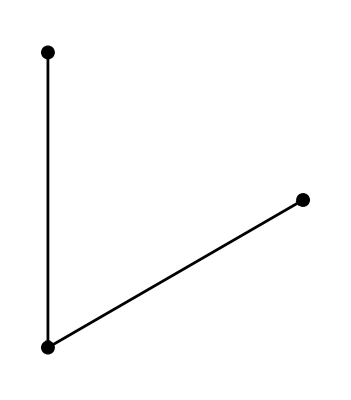
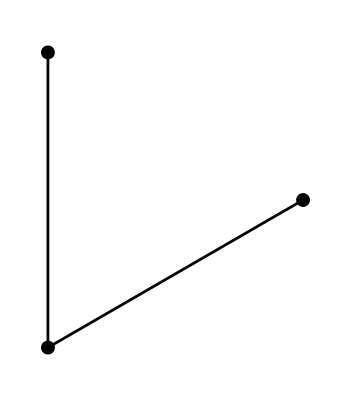

```mathematica
{ShowGraph[FromOrderedPairs[{{1,2},{2,3}}]],ShowGraph[DirectedToUndirected[FromOrderedPairs[{{1,2},{2,3}}]]]}
```

```mathematica
ToOrderedPairs[DirectedToUndirected[FromOrderedPairs[{{1,2},{2,3}}]]]
```

{{2,1},{3,2},{1,2},{2,3}}

```mathematica
DS[{1,2},Cycle[4]]
```

{{2,3},{1,4}}

```mathematica
FDS[{1,2},Cycle[4]]
```

1/4

```mathematica
FDS[{1,2},CompleteGraph[4]]
```

1/3

```mathematica
WnCut[{1,2},Cycle[4]]
```

1

```mathematica
WnCut[{1,2},CompleteGraph[4]]
```

4/3

```mathematica
FindMinimumWnCut[Cycle[4]]
```

{{1.,{1,2}},{1.,{1,4}},{1.,{2,3}},{1.,{3,4}},{1.33333,{1}},{1.33333,{2}},{1.33333,{3}},{1.33333,{4}},{1.33333,{1,2,3}},{1.33333,{1,2,4}},{1.33333,{1,3,4}},{1.33333,{2,3,4}},{2.,{1,3}},{2.,{2,4}}}

```mathematica
FindMinimumWnCut[Cycle[4],{{1},{1,2},{1,2,3},{1,2,3,4}}]
```

```mathematica
GDegree[Cycle[4],1]
```

2

```mathematica
GVol[Cycle[4],{1,2}]
```

4

```mathematica
GVol[Cycle[4]]
```

8

```mathematica
HG[{1,2},Cycle[4]]
```

1/2

```mathematica
HG[{1,2},CompleteGraph[4]]
```

2/3

```mathematica
FindMinimumHG[Cycle[4]]
```

{{0.5,{1,2}},{0.5,{1,4}},{0.5,{2,3}},{0.5,{3,4}},{1.,{1}},{1.,{2}},{1.,{3}},{1.,{4}},{1.,{1,3}},{1.,{2,4}},{1.,{1,2,3}},{1.,{1,2,4}},{1.,{1,3,4}},{1.,{2,3,4}}}

```mathematica
Ncut[{1},Cycle[4]]
```

4/3

```mathematica
Ncut[{},Cycle[4]]
```

0

```mathematica
FindMinimumNcut[Cycle[4]]
```

{{1.,{1,2}},{1.,{1,4}},{1.,{2,3}},{1.,{3,4}},{1.33333,{1}},{1.33333,{2}},{1.33333,{3}},{1.33333,{4}},{1.33333,{1,2,3}},{1.33333,{1,2,4}},{1.33333,{1,3,4}},{1.33333,{2,3,4}},{2.,{1,3}},{2.,{2,4}}}

```mathematica
Ncut[s_,g_]:=Module[{c,s2,v1,v2},
s2=Complement[Table[i,{i,1,V[g]}],s];
v1=GVol[g,s];v2=GVol[g,s2];c=Length[DS[s,g]];
If[v1==0,c/v2,If[v2==0,c/v1,c(1/v1+1/v2)]]];
```

```mathematica
Ncut[{},Cycle[4]]
```

0

```mathematica
TruncateMatrix[{{1,2,3},{4,5,6},{7,8,9}},2]
```

{{0,0,0},{4,5,6},{0,0,0}}

```mathematica
TruncateUptoMatrix[{{1,2,3},{4,5,6},{7,8,9}},2]
```

{{1,2,3},{4,5,6},{0,0,0}}

```mathematica
DelaunayEdges[Vertices[Cycle[5]]]
```

{{1,2},{1,3},{1,5},{2,3},{3,4},{3,5},{4,5}}

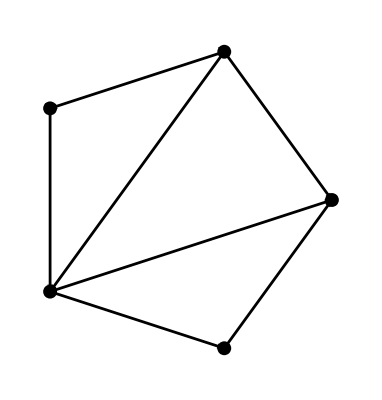

```mathematica
ShowLabeledGraph[FromOrderedPairs[DelaunayEdges[Vertices[Cycle[5]]]]]
```

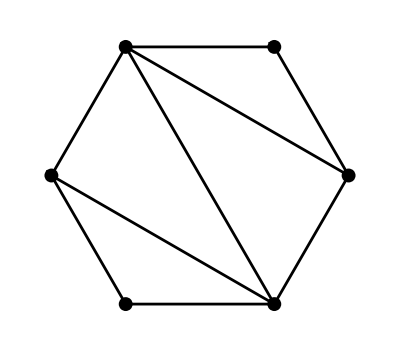

```mathematica
ShowLabeledGraph[DelaunayGraph[Vertices[Cycle[6]]]]
```

```mathematica
Edges[Cycle[5]]
```

{{1,2},{2,3},{3,4},{4,5},{1,5}}

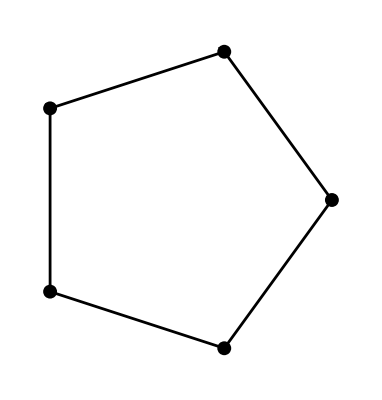

```mathematica
ShowLabeledGraph[CreateGraph[Vertices[Cycle[5]],Edges[Cycle[5]]]]
```

{{0.551886,-0.393259},{0.741625,0.116823},{-0.354993,-0.237024},{0.225804,-0.322781},{-0.789443,0.348371}}

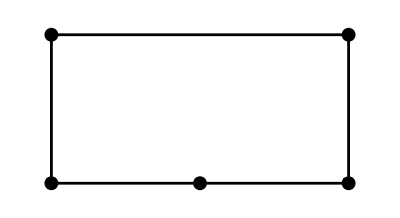

```mathematica
NVertices[5]
```

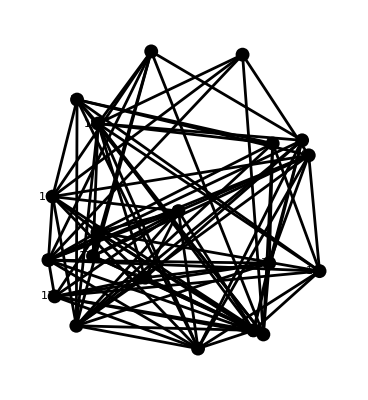

```mathematica
ShowLabeledGraph[NRandomGraph[20,0.5]]
```

```mathematica
Vertices[Cycle[4]]
```

{{0,1.},{-1.,0},{0,-1.},{1.,0}}

```mathematica
CycleVertices[4,Pi/2]
```

{{-1,0},{0,-1},{1,0},{0,1}}

```mathematica
ShowLabeledGraph[Cycle[5]]
```

-Graphics-

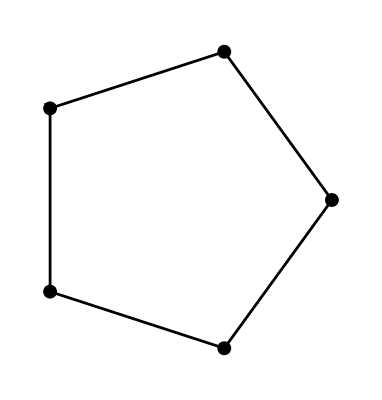

```mathematica
ShowLabeledGraph[CycledGraph[5,2Pi/5]]
```

```mathematica
NMatrixPower[{{1,-1},{1,1}},3]
```

{{-2.,-2.},{2.,-2.}}

```mathematica
MatrixPower[{{1,-1},{1,1}},3]
```

{{-2,-2},{2,-2}}

```mathematica
Diagonalize[{{1,2,3},{4,5,6},{9,8,7}}]//N
```

{17.7593,-5.31482,0.555556}

```mathematica
Eigenvalues[{{1,2,3},{4,5,6},{9,8,7}}]//N
```

{15.3459,-2.3459,0.}

```mathematica
Eigenvectors[{{1,2,3},{4,5,6},{9,8,7}}]//N
```

{{0.30649,0.698437,1.},{-0.605459,-0.487097,1.},{1.,-2.,1.}}

```mathematica
m={{1,2,3},{4,5,6},{9,8,7}}
```

```mathematica
ComplexPower[1+I,1+I]//N
```

0.273957+0.583701 ⅈ

```mathematica
MatrixT[{{1,-1},{1,1}},3]
```

{{-2.,-2.},{2.,-2.}}

```mathematica
ColoringVertex[{{1,2,3},{4,5}}]
```

{{1,2,3,VertexColor→RGBColor[1,0,0]},{4,5,VertexColor→RGBColor[0,0,1]}}

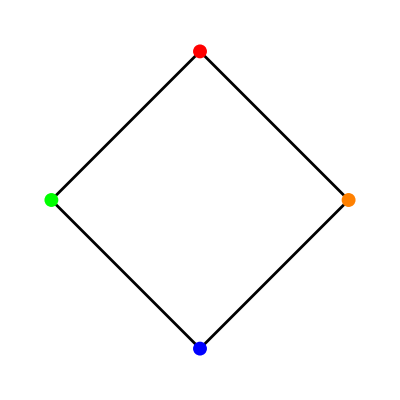

2

```mathematica
ShowGraph[Coloring[Cycle[4]]]
```

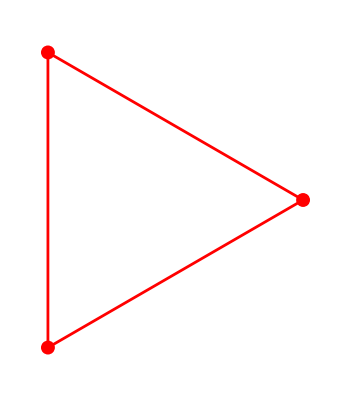
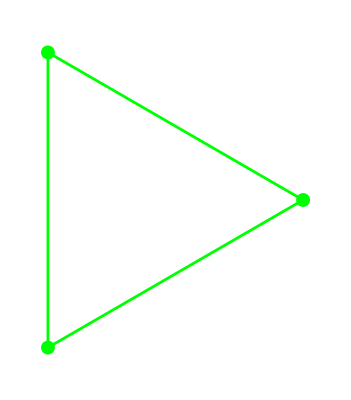
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ShowColoredGraphs[Table[Cycle[3],{5}],{{1,3,5},{2,4}}]
```

```mathematica
Transpose[{Table[i,{i,1,2}],gl}]
```

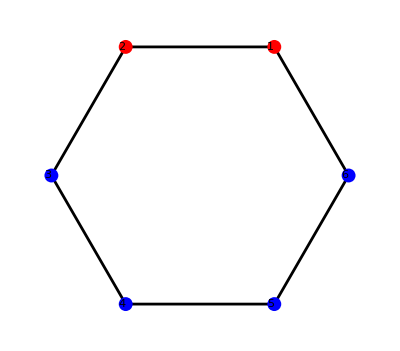

```mathematica
ShowLabeledGraph[ColoringSubset[Cycle[6],{1,2}]]
```

```mathematica
gv=Join[Table[{RandomInteger[5],RandomInteger[5]},{5}],Table[{RandomInteger[5]+5,RandomInteger[5]+5},{5}]]
```

{{5,4},{2,4},{1,4},{1,2},{3,0},{6,6},{8,6},{8,7},{6,5},{9,8}}

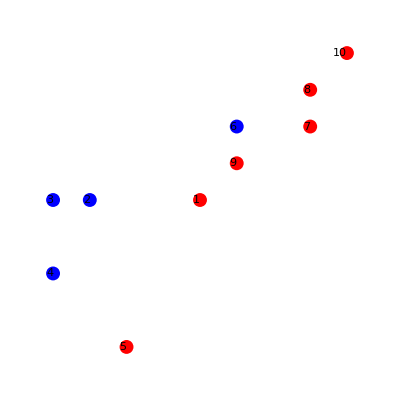

```mathematica
ShowLabeledGraph[SetGraphOptions[CreateGraph[gv,{}],ColoringVertex[PCA3Clustering[gv,2]]]]
```

```mathematica
gv=Table[{RandomInteger[5],RandomInteger[5]},{10}]
```

{{5,3},{2,5},{0,1},{2,0},{0,4},{1,1},{3,2},{4,4},{3,2},{1,3}}

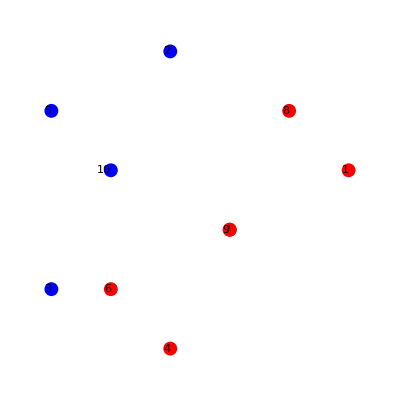

```mathematica
ShowLabeledGraph[SetGraphOptions[CreateGraph[gv,{}],ColoringVertex[PCA3Clustering[gv,2]]]]
```